****************** Must run Hamiltonian_Evolution_2.nb ***************

## Cross Resonance Parameters

ωr1 = ω2
ζ2 → 0
η2 → 0
ϕ2 → 0

```mathematica
HCR[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{htp, h1,h2,h3,h12,h23,h31,h123, Ω1,ωr1,ϕ1, Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31,ζ1,ζ2,ζ3,η1,η2,η3},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];
ζ1=ArcTan[(ω1-ωr1)/Ω1];    ζ2=ArcTan[(ω2-ωr2)/Ω2];    ζ3=ArcTan[(ω3-ωr3)/Ω3];  
η1=√((ω1-ωr1)^2+Ω1^2);  η2=√((ω2-ωr2)^2+Ω2^2); η3=√((ω3-ωr3)^2+Ω3^2);


h12=1/4 ω12 Cos[ζ1]( Cos[ϕ1]  X1.X2  + Sin[ϕ1]  X1.Y2 );
h23=0;
h31=0;

h123=0;

htp =h12+h23+h31+h123;

htp
];
```

```mathematica
UCR[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{utp,ti,ut,ht,et,ψt},
utp=I0[3];
ht=HCR[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
{et,ψt}=Eigensystem[ht];
utp =Transpose[ψt].DiagonalMatrix[ⅇ^(-ⅈ et dt)].Conjugate[ψt];

utp
];
```

ωr1 = ω2
ζ2 → 0  ⇒ ωr2 → ω2
η2 → 0 ⇒ Ω2 → 0 
ϕ2 → 0

```mathematica
ωl={0.5,0.4,0.3*0};
ω2l={0.2,0.15*0,0.07*0};
Ωl={4.6,0.00000001,0.000000001};
ωrl={0.4,0.4,0.3};
ϕl={0.5,0.0,0.22};
Λ=0.01*0;
```

```mathematica
dt=0.1;
t=50.5;
ψ12t=X1.ψ000;
z1l = {};
z2l={};
z3l={};
For[ti=dt,ti≤t,ti+=dt,
ψ12t=UCR[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψ12t;
z1=Conjugate[ψ12t].Z1.ψ12t;
z2=Conjugate[ψ12t].Z2.ψ12t;
z3=Conjugate[ψ12t].Z3.ψ12t;

z1l=Join[z1l,{{ti,z1}}];
z2l=Join[z2l,{{ti,z2}}];
z3l=Join[z3l,{{ti,z3}}];
];
```

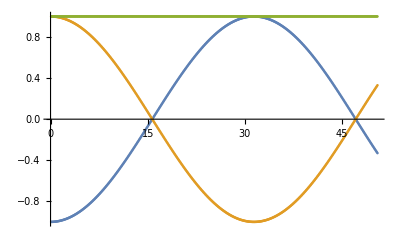

```mathematica
ListPlot[{z1l,z2l,z3l}]
```

### Compare to Hc

Unlike my method, cross-resonance does not turn off the other couplings.  If Λ is large or if ω3 ~ ω2 then there is large error.

```mathematica
ωl={0.5,0.4,0.7};
ω2l={0.2,0.15,0.07};
Ωl={4.6,0.00000001,0.0000001};
ωrl={0.4,0.4,0.7};
ϕl={0.5,0.0,0.0};
Λ=0.01;
```

```mathematica
dt=0.1;
t=50.5;
ψct=X1.ψ000;
z1l = {};
z2l={};
z3l={};
For[ti=dt,ti≤t,ti+=dt,
ψct=Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψct;
z1=Conjugate[ψct].Z1.ψct;
z2=Conjugate[ψct].Z2.ψct;
z3=Conjugate[ψct].Z3.ψct;

z1l=Join[z1l,{{ti,z1}}];
z2l=Join[z2l,{{ti,z2}}];
z3l=Join[z3l,{{ti,z3}}];
];
```

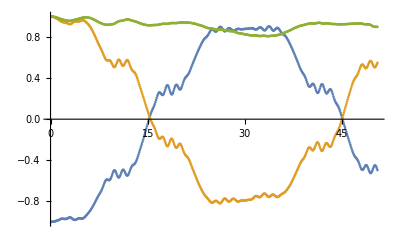

```mathematica
ListPlot[{z1l,z2l,z3l}]
```

### Compare to Ha

```mathematica
ωl={0.5,0.4,0.7};
ω2l={0.2,0.15,0.07};
Ωl={0.3,0.00000001,0.0000001};
ωrl={0.4,0.4,0.7};
ϕl={0.5,0.0,0.0};
Λ=0.01;
```

```mathematica
dt=0.01;
t=50.5;
z1l={};
z2l={};
z3l={};
zc1l={};
zc2l={};
zc3l={};
ψt=X1.ψ000;
ψt=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0].ψt;
ψct=X1.ψ000;
ψct=ψct;
For[ti=dt,ti≤t,ti+=dt,
ψt=Ua[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψt;
ψot=Conjugate[Transpose[Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti]]].ψt;

z1=Conjugate[ψot].Z1.ψot;
z2=Conjugate[ψot].Z2.ψot;
z3=Conjugate[ψot].Z3.ψot;

z1l=Join[z1l,{{ti,z1}}];
z2l=Join[z2l,{{ti,z2}}];
z3l=Join[z3l,{{ti,z3}}];



ψct=Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψct;
ψcot=ψct;

zc1=Conjugate[ψcot].Z1.ψcot;
zc2=Conjugate[ψcot].Z2.ψcot;
zc3=Conjugate[ψcot].Z3.ψcot;

zc1l=Join[zc1l,{{ti,zc1}}];
zc2l=Join[zc2l,{{ti,zc2}}];
zc3l=Join[zc3l,{{ti,zc3}}];
];
```

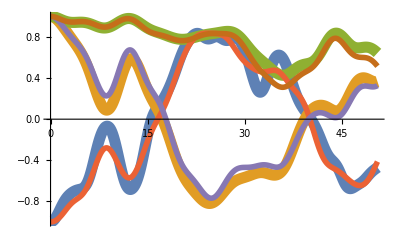

```mathematica
ListPlot[{z1l,z2l,z3l,zc1l,zc2l,zc3l},Joined->True,PlotStyle->{Thickness[0.02],Thickness[0.02],Thickness[0.02],Thickness[0.01],Thickness[0.01],Thickness[0.01]}]
```

### Compare to H

```mathematica
ωl={0.5,0.4,0.7};
ω2l={0.2,0.15,0.07};
Ωl={0.5,0.00000001,0.0000001};
ωrl={0.4,0.4,0.7};
ϕl={0.5,0.0,0.0};
Λ=0.01;
```

```mathematica
dt=0.1;
t=50.5;
z1l={};
z2l={};
z3l={};
zc1l={};
zc2l={};
zc3l={};
z121l={};
z122l={};
z123l={};
ψt=X1.ψ000;
ψt=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0.0].ψt;
ψt=Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0.0].ψt;
ψct=X1.ψ000;
ψ12t=X1.ψ000;
For[ti=dt,ti≤t,ti+=dt,
ψt=U[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψt;
ψot=Conjugate[Transpose[Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti]]].ψt;
ψot=Conjugate[Transpose[Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti]]].ψot;

z1=Conjugate[ψot].Z1.ψot;
z2=Conjugate[ψot].Z2.ψot;
z3=Conjugate[ψot].Z3.ψot;

z1l=Join[z1l,{{ti,z1}}];
z2l=Join[z2l,{{ti,z2}}];
z3l=Join[z3l,{{ti,z3}}];



ψct=Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψct;
ψcot=ψct;

zc1=Conjugate[ψcot].Z1.ψcot;
zc2=Conjugate[ψcot].Z2.ψcot;
zc3=Conjugate[ψcot].Z3.ψcot;

zc1l=Join[zc1l,{{ti,zc1}}];
zc2l=Join[zc2l,{{ti,zc2}}];
zc3l=Join[zc3l,{{ti,zc3}}];

ψ12t=U12[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψ12t;
ψ12ot=ψ12t;

z121=Conjugate[ψ12ot].Z1.ψ12ot;
z122=Conjugate[ψ12ot].Z2.ψ12ot;
z123=Conjugate[ψ12ot].Z3.ψ12ot;

z121l=Join[z121l,{{ti,z121}}];
z122l=Join[z122l,{{ti,z122}}];
z123l=Join[z123l,{{ti,z123}}];
];
```

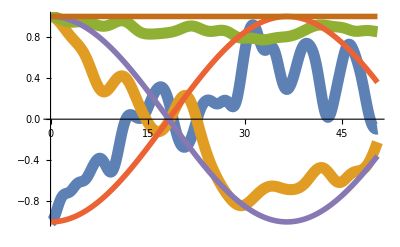

```mathematica
ListPlot[{z1l,z2l,z3l,z121l,z122l,z123l},Joined->True,PlotStyle->{Thickness[0.02],Thickness[0.02],Thickness[0.02],Thickness[0.01],Thickness[0.01],Thickness[0.01]}]
```